## Lab 2

Enter the definitions for f(x)=3 x^2 +2x +1, g(x)=2(x-1)^2, and h(x)=1-2x. Then, evaluate the following expressions. If helpful, apply Simplify to a result.

f(g(g(5))

```mathematica
f[x_]= 3x^2+2x+1
g[x_]=2(x-1)^2
h[x_]= 1-2x
```

1+2 x+3 x^2

2 (-1+x)^2

1-2 x

```mathematica
f[g[g[5]]]
```

11086097

g(f(h(x)))

```mathematica
Simplify [g[f[h[x]]]]
```

2 (5-16 x+12 x^2)^2

h(h(h(x-2)))

```mathematica
Simplify [h[h[h[x-2]]]]
```

19-8 x

f(h(f(g(x^2+1))))

```mathematica
Simplify [f[h[f[g[x^2+1]]]]]
```

2 (1+16 x^4+144 x^8+576 x^12+864 x^16)

Using If, define the piecewise-defined function f(x)=Piecewise[{{6-sin(x+1),, x≤-1}, {2 x^2-3x+1,, -1<x<2}, {3x-3,, x≥2}}], and plot its graph on the interval [-4,5].

```mathematica
f[x_]:=If[x≤ -1,6-Sin[x+1],If[x≥ 2,3x-3,2 x^2-3x+1]]
```

```mathematica
Function[x,If[x≤-1,6-Sin[x+1],If[x≥2,3 x-3,2 x^2-3 x+1]]]
```

Function[x,If[x≤-1,6-Sin[x+1],If[x≥2,3 x-3,2 x^2-3 x+1]]]

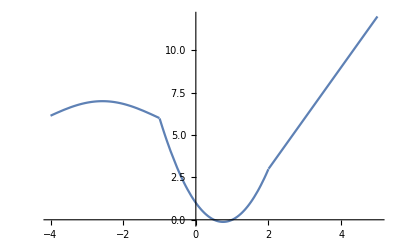

```mathematica
Function[x,If[x≤-1,6-Sin[x+1],If[x≥2,3 x-3,2 x^2-3 x+1]]]
Plot[{f[x]}, {x,-4,5}]
```

Using Which, redo Question 2.

```mathematica
f[x_]:= Which[ x≤-1, 6-Sin[x+1], -1<x<2, 2 x^2-3x+1, x≥2, 3x-3]
```

```mathematica
Function[x,Which[x≤-1,6-Sin[x+1],-1<x<2,2 x^2-3 x+1,x≥2,3 x-3]]
```

Function[x,Which[x≤-1,6-Sin[x+1],-1<x<2,2 x^2-3 x+1,x≥2,3 x-3]]

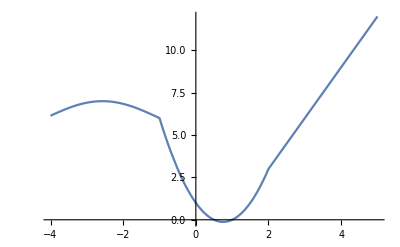

```mathematica
Plot[{f[x]},{x,-4,5}]
```

Using Piecewise, redo Question 2.

```mathematica
f[x_]:=Piecewise[{{6-Sin[x+1], x≤-1}, {2 x^2-3x+1, -1<x<2}, {3x-3, x≥2}}]
```

```mathematica
Function[x,Piecewise[{{6-Sin[x+1],x≤-1},{2 x^2-3 x+1,-1<x<2},{3 x-3,x≥2}}]]
```

Function[x,Piecewise[{{6-Sin[x+1], x≤-1}, {2 x^2-3 x+1, -1<x<2}, {3 x-3, x≥2}}]]

```mathematica
Plot[{f[x]}, {x,-4,5}]
```

-Graphics-

Plot each function. Explain why non-periodic functions like e^x and ln x can be made periodic here. Tips: Exam how the value of, say, x-Round[x], varies. You need to choose a proper interval for the function Plot.

f(x)=ⅇ^([x-Round(x)]^3)

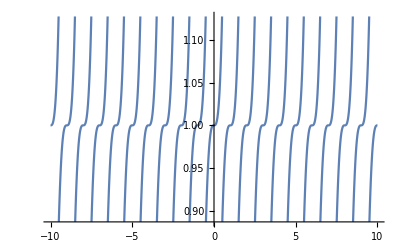

```mathematica
Plot[ⅇ^({x-Round[x]}^3), {x,-10,10}, PlotRange->Automatic]
```

g(x)=ln[x-Floor(x)]^2

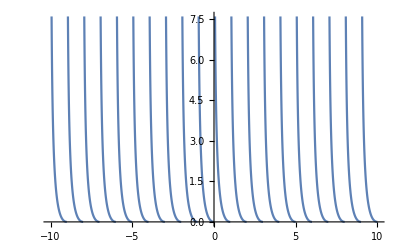

```mathematica
Plot[ Log[x-Floor[x]]^2, {x,-10,10}, PlotRange->Automatic]
```

Plot on a figure the graphs of f(x)=3sin x-2cos x and g(x)=1/2(x-1)^2-3 over the interval [-2π,2π].

```mathematica
f[x_]=3Sin[x]-2Cos[x]
g[x_]=((1/2)[x-1])^2-3
```

-2 Cos[x]+3 Sin[x]

-3+(1/2[-1+x])^2

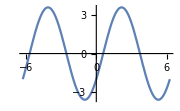

```mathematica
Plot[{f[x],g[x]},{x,-2Pi,2Pi}, ImageSize-> 180]
```

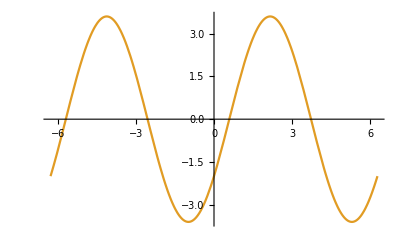

```mathematica
Plot[{((1/2)[x-1])^2-3,3Sin[x]-2Cos[x]},{x,-2Pi,2Pi}]
```

Redo Question 6 with the region between the curves of f(x) and g(x) shaded.

Redo Question 6 with the region enclosed by the curves of f(x) and g(x) shaded. Tips: You may refer to the first example in the section, Drawing two functions with enclosed region shaded, in this Unit.

Using Animate, make animation of the graph of f(x)=a (x-h)^2+k, where a,h, and k are parameters which each vary in the range from -3 to 3.

```mathematica
f[x_]:= a[x-h]^2+k
```

k+

```mathematica
Animate[Plot[a[x-h]^2+k,{x,-10,10},ImageSize->160],{k,-3,3},{a,-3,3},{h,-3,3}]
```

Using Manipulate, redo Question 9.

```mathematica
Manipulate[Plot[a[x-h]^2+k,{x,-10,10},ImageSize->160],{k,-3,3},{a,-3,3},{h,-3,3}]
```